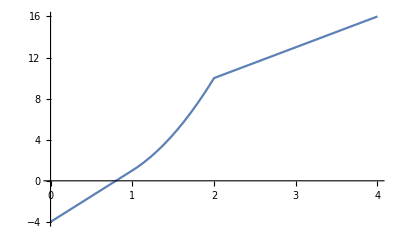

```mathematica
f[x_]:=5*x-4/;0<x≤1
f[x_]:=4*x^2-3x/;1<x<2
f[x_]:=3*x+4/;x≥2
Plot[f[x],{x,0,4}]
```

```mathematica
lhd=Limit[(f[1+h]-f[1])/h,h->0,Direction->1]/.x->1
rhd=Limit[(f[1+h]-f[1])/h,h->0,Direction->1]/.x->1
lhd==rhd
```

Limit[(-1+f[1+h])/h,h→0,Direction→1]

Limit[(-1+f[1+h])/h,h→0,Direction→1]

True